-(2 ArcTanh[(4+Tan[x/2])/(√15)])/(√15)

0.413328

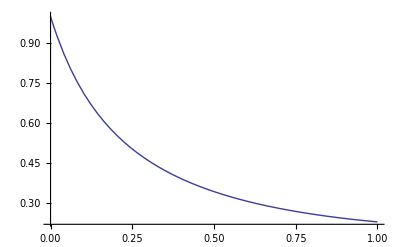

Riemann

0.335685

0.18785

Trapecios

0.432053

0.0453035

Simpson

0.416528

0.0077414

```mathematica
f[x_]=1/(4 Sin[x]+1);
(*f[x_]=ⅇ^(-x^2)*)

∫f[x]ⅆx
Int=∫_0^1 f[x]ⅆx//N
a=0;
b=1;
n=4;
Plot[f[x],{x,a,b}]

Print["Riemann"]
suma=0;
dx=(b-a)/n;
For[i=1,i≤n,i++,
suma=suma+f[a+dx*i]
]
resultado=suma*dx//N
Error=Abs[(Int-resultado)/Int]//N

Print["Trapecios"]
suma=0;
dx=(b-a)/n;
For[i=1,i≤n-1,i++,
suma=suma+f[a+dx*i]
]
resultado=(f[a]+f[b]+2 suma)dx/2//N
Error=Abs[(Int-resultado)/Int]//N

Print["Simpson"]
sumapares=0;
sumaimpares=0;
For[i=1,i≤ n/2-1,i++,
sumapares=sumapares+f[a+(dx*2i)]
]
For[i=1,i≤ n/2,i++,
sumaimpares=sumaimpares+f[a+(dx*(2i-1))]
]
resultado=(f[a]+4 sumaimpares+2sumapares+f[b])dx/3//N
Error=Abs[(Int-resultado)/Int]//N
```